Problem 9.20 (a)

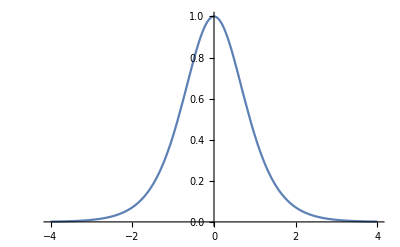

```mathematica
Plot[Sech[x]^2,{x,-4,4},PlotRange->{0,1}]
```

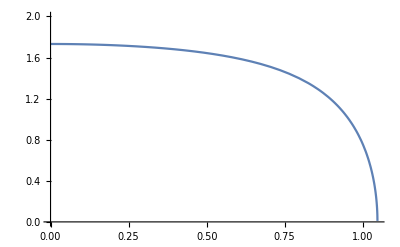

```mathematica
Plot[√(4-1/Cos[x]^2),{x,0,1.5},PlotRange->{0,2}]
```

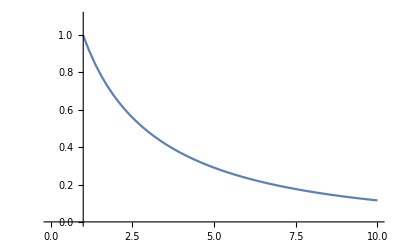

```mathematica
Plot[ⅇ^(1-√x),{x,1,10},PlotRange->{0,1.1},AxesOrigin->{1,0}]
```

Problem 9.20 (c)

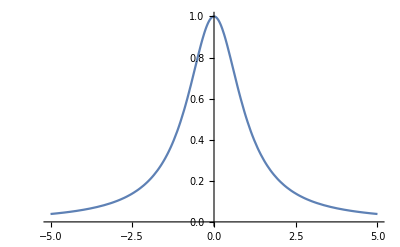

```mathematica
Plot[1/(1+x^2),{x,-5,5},PlotRange->{0,1}]
```

```mathematica
w[x_]:=1-1/x
```

```mathematica
L[x_]:=√(w[x]/(1-w[x]))EllipticE[ArcSin[√w[x]],1/w[x]]
```

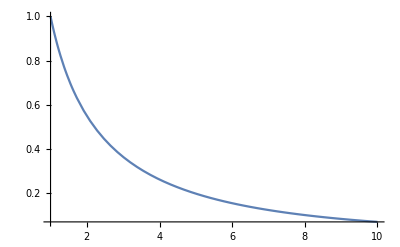

```mathematica
Plot[ⅇ^(-L[x]),{x,1,10}]
```